## Subradiance-protected excitation spreading for collimated photon emission

P. Huft
See paper by K. Ballantine, J. Ruostekoski

## personal notes

### Questions

Why can a system which is excited with a single photon be adequately described by classical E&M?

The collective mode which is predominantly coupled by the initial excitation (after rotating the polarization to be normal to the atom grid plane) decays slowly, i.e. is subradiant, while other modes decay superradiantly. Why do these other modes see an a higher rate of decay than independent decay? Does it just “come out of the math” as with the √N enhancement of ensemble Rabi flopping?

## setup

System description: atomnum two-level atoms arranged in a 2D square grid with equal periodicity in x and y. The lower level is has only one angular momentum state (J=0) while the upper state has three Zeeman sublevels (J=1).

```mathematica
(*PHYSICAL CONSTANTS*)
ℏ = 6.62607015*^-34/(2π);
μ0 =4π*10^-7;
c = 299792458;
ϵ0 = 1/(c^2 μ0);
ee = 1.602*^-19; (*electron charge*)
a0 = 5.27*^-11; (*Bohr radius*)
(*PARAMETERS and other DEFINITIONS*)
atomnum = 5*5; (*should be an odd perfect square*)
J = 1; (*upper level total angular momentum*) 
λ = 7.8*10^-7;
k =2π/λ;
matelem = ee a0; (*just assume a general matrix element is of this order for now.*)
γ = matelem^2 k^3/(6 π ℏ ϵ0); (*single two-level atom linewidth*)
a=0.75 λ; (*atomic grid spatial period*)
pol = Range[3];(*pol[[μ]]/.u->1,2,3 for polarization σ=-1,0,+1 *)
Subscript[Δ, μ_]:= {0,0,0}[[μ]]; (*no Zeeman splitting for now*)
deg = 2J+1;
dim = deg*atomnum; (*Hamiltonian shape is dim x dim, with state vector = dim*)

(*FUNCTIONS*)
idx[i_,j_,n_]:=(i-1)n+j//Simplify; (*get 1D atom idx from 2D coordinate indices*)
Subscript[r, i_,j_]:={Mod[j-1,n]-Mod[i-1,n],Floor[(j-1)/n]-Floor[(i-1)/n]}/.n->atomnum;(*distance between atoms i,j in units lattice spacing*)
sphrWave[x_,y_,z_]:=(ⅇ^(ⅈ k √(x^2+y^2+z^2)))/(4 π √(x^2+y^2+z^2));(*spherical wave*)
Subscript[Kδ, μ_,ν_]:=KroneckerDelta[SymbolName[μ],SymbolName[ν]];(*symbolic Kronecker delta*)
dipOp[α_,β_]=(D[#,α]D[#,β]-Subscript[Kδ, α,β] Laplacian[#,{x,y,z}]-Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)])&; (*derivative op in the expression for positive freq. component of monochromatic dipole radation*)
Subscript[G, α_,β_]:=dipOp[α,β][sphrWave[x,y,z]];
(*element (α,β) of the positive frequency compenent of monochromatic dip. radiation*)
GTensor = Table[Subscript[G, α,β]+(Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)])/3,{α,{x,y,z}},{β,{x,y,z}}];
Subscript[e, μ_] :={{1,0,0},{0,1,0},{0,0,1}}[[μ]]; (*generic basis vector set*)
Subscript[ecart, μ_]:={1/(√2){1, -1, 0}, -ⅈ/(√2){1, 1, 0}, {0, 0, 1}}[[μ]];(*x,y,z in spherical basis*)
Subscript[esphr, μ_]:={1/(√2){1,ⅈ,0},-1/(√2){1,-ⅈ,0},{0,0,1}}[[μ]];(*-1,+1,0 in cartesian basis*)
```

Restricting this problem to the single-excitation subspace, the Hamiltonian matrix elements are: H_(3j-1+ν,3k-1+ν)=H_νμ^(jk)=Δ_μ δ_jk δ_μν+Ω_μν^(jk)(1-δ_jk)+ⅈ γ_μν^(jk), where μ,ν specify polarization in a spherical basis and j,k are the atom indices in the 2D grid. The dynamics in this subspace are coherent, but H is non-Hermitian, so there is dissipation as the excitation diffuses into the collective ground state.

- Δ,γ values used are arbitrary with the given choice of plot units.

## Linewidths vs lattice spacing

```mathematica
ipmode = Flatten@Array[Subscript[ecart, 2]&,atomnum];(*in-plane state: each atom excited with P=y*)
fmode =Flatten@Array[Subscript[ecart, 1]&,atomnum];(*ferromagnetic state: each atom excited with P=x, all in phase*)
afmode =Flatten@Array[(-1)^# Subscript[ecart, 1]&,atomnum];(*antiferromagnetic state: every atom has P=x, but alternating phases by π*)
modelist = {(*{ipmode,"In-plane",Subscript[e, 2]},*){fmode,"Ferromagnetic",Subscript[e, 1]},{afmode,"Antiferromagnetic",(-1)^k Subscript[e, 1]}};(*{mode, name, polarization of kth atom in cartesian basis}*)
soln=Array[{}&,Length[modelist]];
```

```mathematica
(*calculate the collective linewidths for modelist modes as a function of lattice spacing*)
res = Timing[
For[d=0.01,d<1,d=d++(*0.05*),(*loop over fractional lattice period*)
For[mode=1,mode<Length[modelist]+1,mode++,
e[k_]=modelist[[3]];
(*build the Hamiltonian*)
Hfull = Array[Subscript[H, ##]&,{dim,dim}];
For[i=1,i<atomnum+1,i++,
For[j=1,j<atomnum+1,j++,
For[ν=1,ν<deg+1,ν++,
For[μ=1,μ<deg+1,μ++,
u=d λ Subscript[r, i,j];
v= (e[i]*.GTensor.e[j])/.z->0 //ComplexExpand;(*x polarized for now*)
Ωμνij = If[i==j,0,(6 π γ)/k^3 Re[v/.{x-> u[[1]],y-> u[[2]]}]];
γμνij=Piecewise[{{γ,i==j&& μ==ν},{0,i==j},{(6 π γ)/k^3 Im[v/.{x-> u[[1]],y-> u[[2]]}],i!=j&& μ!=ν}}];
Hfull[[3(i-1)+ν,3(j-1)+μ]]= Subscript[Δ, μ] KroneckerDelta[i,j]KroneckerDelta[μ,ν]+Ωμνij(1-KroneckerDelta[i,j])+ⅈ γμνij;
];
];
];
];
(*find the linewidth of eigenmode which most nearly overlaps the state vector of interest, e.g. the ferromagnetic excitation*)
{evals,evecs} = Eigensystem[Hfull];
overlap = {};
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[modelist[[mode,1]].evecs[[i]]]}]
];
maxIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
(*Print[StringForm["evals[[maxIdx]]: ``, Im[evals[[maxIdx]]]: ``, Log10[Im[evals[[maxIdx]]]/γ]: ``",evals[[maxIdx]],Im[evals[[maxIdx]]],Log10[Im[evals[[maxIdx]]]/γ]]]*)
AppendTo[soln[[mode]],{d,Log10[Abs[Im[evals[[maxIdx]]]/γ]]}];
Print[StringForm["solved for linewidth of `` mode",modelist[[mode]]]]
];
];
];
StringForm["simulation took `` minutes",Floor[res[[1]]/60]]
```

```mathematica
soln
```

{{},{}}

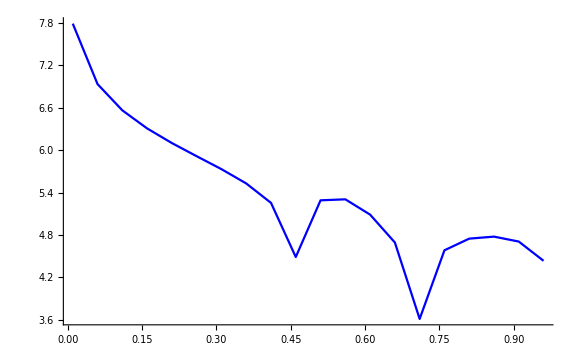

```mathematica
markers = {Graphics[{Blue, Disk[]}],Graphics[{Red,Rectangle[]}],Graphics[{Green, Disk[]}]};
colors = {Blue,Red,Green};
plots = {};
For[lidx=1,lidx<Length[soln]+1,lidx++,
AppendTo[plots,ListPlot[soln[[lidx]],PlotLegends->modelist[[lidx,2]],(*PlotMarkers->{markers[[lidx]],0.02}*)Joined->True,PlotStyle->colors[[lidx]]]];
]
Show[plots,PlotRange->All,ImageSize-> Large]
```

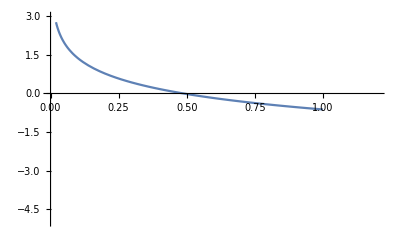

```mathematica
Plot[Log10[3/(4π d^2)],{d,0.02,1},PlotRange->{{0,1.2},{-5,3}}]
```

```mathematica
Clear[lidx]
ListPlot[soln[[lidx]][[45;;75]],PlotLegends->modelist[[lidx,2]],PlotMarkers->{markers[[lidx]],0.02}]/.lidx-> 1
```

```mathematica
soln[[1]][[45;;75]]
```

{{0.45,4.79181},{0.46,4.48744},{0.47,3.4538+1.36438 ⅈ},{0.48,4.61247+1.36438 ⅈ},{0.49,4.9464+1.36438 ⅈ},{0.5,5.16483+1.36438 ⅈ},{0.51,5.28967+1.36438 ⅈ},{0.52,5.34013+1.36438 ⅈ},{0.53,5.35273+1.36438 ⅈ},{0.54,5.34681+1.36438 ⅈ},{0.55,5.32947+1.36438 ⅈ},{0.56,5.30389+1.36438 ⅈ},{0.57,5.27172+1.36438 ⅈ},{0.58,5.23382+1.36438 ⅈ},{0.59,5.19057+1.36438 ⅈ},{0.6,5.14201+1.36438 ⅈ},{0.61,5.08786+1.36438 ⅈ},{0.62,5.02755+1.36438 ⅈ},{0.63,4.96008+1.36438 ⅈ},{0.64,4.88391+1.36438 ⅈ},{0.65,4.7966+1.36438 ⅈ},{0.66,4.69411+1.36438 ⅈ},{0.67,4.56929+1.36438 ⅈ},{0.68,4.4076+1.36438 ⅈ},{0.69,4.17182+1.36438 ⅈ},{0.7,3.69528+1.36438 ⅈ},{0.71,3.61686},{0.72,4.09533},{0.73,4.30129},{0.74,4.42869},{0.75,4.51781}}

True

## radiation in the time domain

```mathematica
(*initialize the state vector. excite central 9 atoms in m=0 states*)

(*state = Array[Subscript[b, ##]&,dim];
excitedIdcs = Flatten@Table[(deg*atomnum-1)/2+deg*√atomnum i+deg j-1,{i,{-1,0,1}},{j,{-1,0,1}}];
state[[excitedIdcs]]=1; *)
```

## tests

pick out element from G depending on the dressing polarization of atoms i,j. Ferromagnetic:

```mathematica
Clear[i]
```

```mathematica
e[k_]:=Subscript[e, 1](*k is the atom number*)
```

```mathematica
e[2]
```

{1,0,0}

Anti-ferromagnetic:

```mathematica
e[k_]:=(-1)^k Subscript[e, 1]
```

In-plane:

```mathematica
e[k_]:=Subscript[e, 2];
```

```mathematica
duh = {x,x^2}
```

{x,x^2}

```mathematica
f[x_]=duh[[2]]
```

```mathematica
g[x_]=duh[[1]]
```

x

```mathematica
g[2]
```

2

made a mistake in my polarization basis. no zeeman splitting, and ferro/anti-ferro states have x polarizations. use spherical basis for atomic states; need to work in Jz basis because this is good quantum number here.

Px excitation is superposition of P_(-1,+1). Likewise for Py.  X=1/(√2)(-1-+1), Y=-ⅈ/(√2)(-1++1). So with the basis {-1,+1,|0⟩}, the x,y,z states are:

```mathematica
1/(√2)(Subscript[esphr, 1]-Subscript[esphr, 2]) (*recover x*)
-ⅈ/(√2)(Subscript[esphr, 1]+Subscript[esphr, 2]) (*recover y*)
{1,0,0}
{0,1,0}
```

```mathematica
period = 0.5 λ;
μ=1;ν=1;i=2;j=2;
G = Subscript[dipRadKernel, μ,ν,i,j,period]
```

{0,2.11678×10^6}

```mathematica
Ωμνij=(6 π γ)/k^3 G[[1]];
γμνij =(6 π γ)/k^3 G[[2]];
Hfull[[3(i-1)+ν,3(j-1)+μ]]= Subscript[Δ, μ] KroneckerDelta[i,j]KroneckerDelta[μ,ν]+Ωμνij(1-KroneckerDelta[i,j])+ⅈ γμνij
```

0.+1.61584×10^-7 ⅈ

```mathematica
γ
```

2.11678×10^6

```mathematica
(*Find the basis eigenvalues of interest by diagonalizing the Hamiltonian and then finding the overlap of the resultant e-vecs with the desired basis vectors*)
{evals,evecs} = Eigensystem[Hfull];
```

```mathematica
fmode =Flatten@Array[Subscript[ecart, 1]&,9](*ferromagnetic state: each atom excited with polarization x:*)
(*afmode = Array[KroneckerDelta[,Mod[#,2(2J+1)]]]*)
```

{1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0,1/(√2),-1/(√2),0}

```mathematica
afmode =Flatten@Array[(-1)^# Subscript[ecart, 1]&,9]
```

{-1/(√2),1/(√2),0,1/(√2),-1/(√2),0,-1/(√2),1/(√2),0,1/(√2),-1/(√2),0,-1/(√2),1/(√2),0,1/(√2),-1/(√2),0,-1/(√2),1/(√2),0,1/(√2),-1/(√2),0,-1/(√2),1/(√2),0}

```mathematica
ipmode = Flatten@Array[Subscript[ecart, 2]&,9]
```

{-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0,-ⅈ/(√2),-ⅈ/(√2),0}

```mathematica
{evals,evecs} = Eigensystem[Hfull];
overlap = {};(*list with entries {idx, overlap coefficient}*)
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[fmode.evecs[[i]]]}]
]
maxIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
linewidth=Log10[Im[evals[[maxIdx]]]/γ];
```

7.33422

```mathematica
period
```

1.05

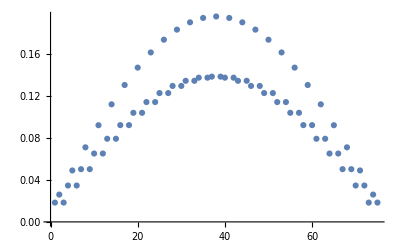

```mathematica
ListPlot[Re[evecs[[maxIdx]]]]
```

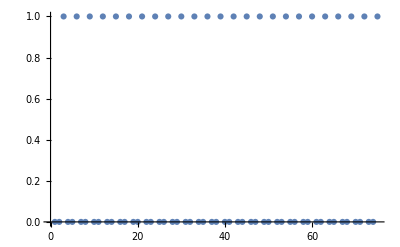

```mathematica
ListPlot[fmode]
```

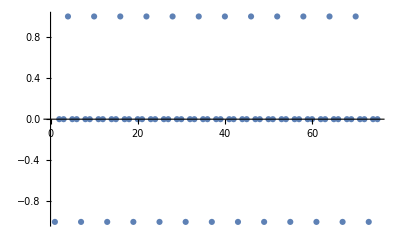

```mathematica
ListPlot[afmode]
```

```mathematica
fmode = Array[KroneckerDelta[2,Mod[#,3]]&,dim];(*anti-ferromagnetic state*)
```

```mathematica
afmode= Array[Boole[(u==1|| u==0)/.u-> Mod[#,6]]&,15]
```

{1,0,0,0,0,1,1,0,0,0,0,1,1,0,0}

```mathematica
Array[Boole[(u==1|| u==0)/.u-> Mod[#,6]]&,12]
```

{1,0,0,0,0,1,1,0,0,0,0,1}

```mathematica
1,2,3,4,5,6,7,8,9,10,11,12,13,14,15
1,0,0,0,0,1,1,0,0,0,0,1,1,0,0
```

every other group of three, use KroneckerDelta[1or2,Mod[#,3]]] to set value to 1.

Build anti/ferromag. states, and then calculate overlap with a given basis vector list

```mathematica
fmode = Array[KroneckerDelta[2,Mod[#,3]]&,9]
```

```mathematica
%
```

{299792458,599584916,899377374,1199169832,1498962290,1798754748,2098547206,2398339664,2698132122}

Check my grid mapping. 2D grid, but only one index to specify atoms

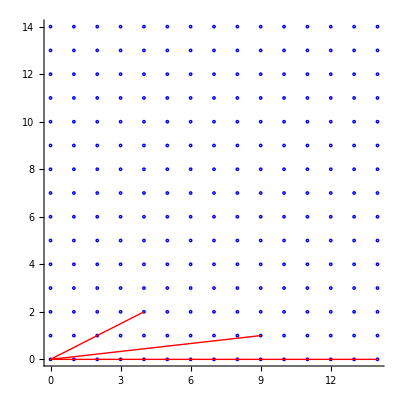

```mathematica
num=atomnum;
a=1;(*0.7;*)
r[i_,j_] :=Graphics[{Red,Line[{a{Mod[i-1,num], Floor[(i-1)/num]},a{Mod[j-1,num],Floor[(j-1)/num]}}]}];
Show[Table[Graphics[{Blue,Circle[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}],{i,Range[num^2]}],Table[r[1,j],{j,{15,25,35}}],(*PlotLegends-> Placed[{"hi"},{1/(a num)//N,1/(a num)//N}],*) Axes->True,PlotRange->{{0,a (num-1)},{0,(a num-1)}}]
```

What 1D atom idx corresponds to (i,j)?

```mathematica
idx[i_,j_,n_]:=(i-1)n+j//Simplify;
```

```mathematica
idx[2,2,n]
```

2+n

```mathematica
idx[1,1,n]//Simplify
```

(2+n)/2

```mathematica
Solve[{n+2== 2 (α  + β),n==α +β n },{α,β} ]
```

{{α→n^2/(2 (-1+n)),β→-(2-n)/(2 (-1+n))}}

```mathematica
Clear[i,j]
```

```mathematica
{Mod[i-1,num],Floor[(i-1)/num]}/.{i-> 2,j-> 2}
```

{1,0}

```mathematica
1/(a num)//N
```

0.0666667

```mathematica
Legended
```

```mathematica
r[i_,j_] :=a{Mod[j-1,num]-Mod[i-1,num],Floor[(j-1)/num]-Floor[(i-1)/num]};
```

```mathematica
r[1,15]
```

{2.8,1.4}

```mathematica
υ = Table[x^2+y^2,{x,{-1,0,1}},{y,{-1,0,1}}]
```

{{2,1,2},{1,0,1},{2,1,2}}

```mathematica
{1,0,1}.υ
```

{4,2,4}